## Meshing The Drums

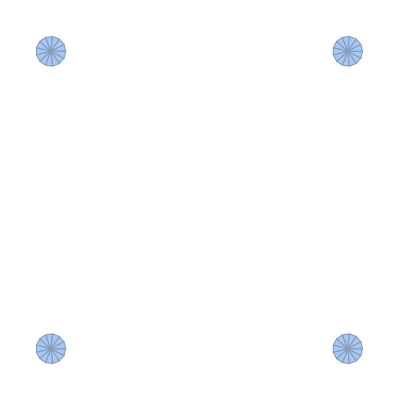

```mathematica
{d,r}={10,1};
DiscretizeRegion[
RegionUnion[
Disk[{-d,-d},r],
Disk[{-d,  d},r],
Disk[{  d, d},r],
Disk[{d,-d},r]]
]
```

```mathematica
ConvexHullMesh
```

ConvexHullMesh